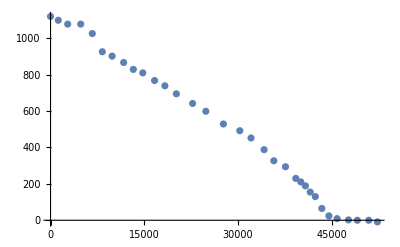

```mathematica
lijst={17.23365217085011,78.95045670201213,17.22756463594287,78.96417314033498,17.2210202389087,78.97669457573872,17.22341927492902,78.98853363636476,17.24011271934415,79.00053803390264,17.24602888468873,79.01156080428402,17.21634641619203,79.02379173745192,17.20349770902566,79.04233511640368,17.19850273235477,79.05887269517164,17.20165549734232,79.07320406625378,17.21129922824315,79.08714070076296,17.23413104314881,79.10306183421177,17.26435761086583,79.11569979233764,17.29901127717955,79.12758180657379,17.32627156368064,79.14367984770769,17.32337716465245,79.15841870198942,17.30753663208706,79.17457612246113,17.28473417332494,79.19744177428109,17.2770883953177,79.2163836755896,17.2729878423019,79.24151571885166,17.26030337833036,79.26489796524422,17.26320226081632,79.28094627353214,17.27477215795971,79.29958110843093,17.28669022000784,79.3133260816973,17.3137865940824,79.3292431985719,17.35212428458879,79.34214419960024,17.38061127419577,79.347052433869,17.41593013565234,79.34822281684831,17.45206343371408,79.34971771765673,17.49169700241167,79.350277855451,17.53794192192042,79.35400766574506,17.58245613247664,79.35988077722351,17.63643346572776,79.36620204123132,17.69376102314247,79.37845164316973,17.73139144715994,79.38922334457679,17.77722232718284,79.40316597996865,17.80535594259288,79.41451868435703};
lijst2=Table[{lijst[[i+1]],lijst[[i]]},{i,1,Length[lijst],2}];
lijst3=GeoElevationData[GeoPosition[lijst2]]["Magnitudes"];
lijst4=Prepend[lijst2,lijst2[[1]]];
lijst5=Table[GeoDistance[lijst4[[i-1]],lijst4[[i]]],{i,2,Length[lijst4]}];
lijst6=QuantityMagnitude[lijst5,"Meters"];
lijst7=Table[Sum[lijst6[[j]],{j,1,i}],{i,1,Length[lijst6]}];
lijst8=Table[{lijst7[[i]] - lijst7⟦5⟧,lijst3[[i]]},{i,5,Length[lijst3]}];
ListPlot[lijst8]
Export[NotebookDirectory[]<>"glacierelevationdata.txt", lijst8, "CSV"]
```